0.5

0.1

0.05

{{kIV→16.5433,kPI→12.0307,kII→16.6606,kVI→16.5433,kIP→12.0307}}

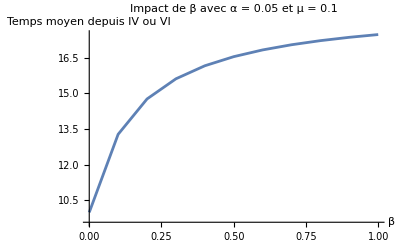

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

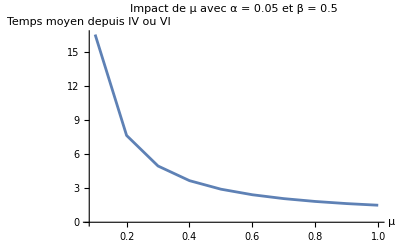

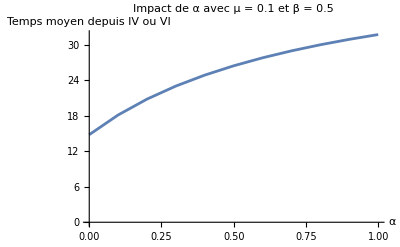

```mathematica
(*---------------------------- Question 1.4 ---------------------------  *)

(*Temps moyen nécessaire pour l'eradication du virus*)
b = 0.5  (* beta *)
m = 0.1 (* mu *)
a = 0.05 (* alpha *)

equations[b_,m_,a_]:={kIV==1+(1-b)*(1-m)*kIV+(m*b)*kPI+b*(1-m)*kII,kPI==1+(1-m)*(1-a)*kPI+a*(1-m)*kVI,
kII==1+(1-m)^2*kII+m*(1-m)*kIP+m*(1-m)*kPI,
kVI==1+(1-b)*(1-m)*kVI+b*(1-m)*kII+(m*b)*kIP,
kIP==1+(1-m)*(1-a)*kIP+a*(1-m)*kIV};

Solve[equations[b,m,a],{kIV,kPI,kII,kVI,kIP}]

(*Graphe : Impact des paramètres*)
(* -- Le code suivant est utilisé pour la réalisation des graphiques -- *)
solveEq[b_,m_,a_]:=kIV/. Solve[equations[b,m,a],{kIV,kPI,kII,kVI,kIP}][[1]];

(*Intervalle des parametres*)
valuesOfParam=Range[0.0,1,0.1];

(*Impact de Beta sur le temps moyen*)
ListLinePlot[Table[{b,solveEq[b, m, a]},{b,valuesOfParam}],AxesLabel->{"β","Temps moyen depuis IV ou VI "},PlotRange->All,PlotLabel->"Impact de β avec α = 0.05 et μ = 0.1"]

(*Impact de Mu sur le temps moyen*)
ListLinePlot[Table[{m,solveEq[b, m, a]},{m,valuesOfParam}],AxesLabel->{"μ","Temps moyen depuis IV ou VI "},PlotRange->All,PlotLabel->"Impact de μ avec α = 0.05 et β = 0.5"]

(*Impact de Alpha sur le temps moyen*)
ListLinePlot[Table[{a,solveEq[b, m, a]},{a,valuesOfParam}],AxesLabel->{"α","Temps moyen depuis IV ou VI "},PlotRange->All,PlotLabel->"Impact de α avec μ = 0.1 et β = 0.5"]
```

```mathematica
6,44.67763584189576,40.93885957604367,40.93885957604367,19.999999999999982,19.999999999999982,29.743589743589716,45.61279274275664}
```

{{kIV→965305/21606,kPI→884525/21606,kII→492755/10803,kPV→20,kVI→965305/21606,kPP→1160/39,kIP→884525/21606,kVP→20}}

0.5

0.05

0.05

{{kIV→37.8469,kPI→28.6947,kII→38.2153,kVI→37.8469,kIP→28.6947}}

```mathematica
0.
```

0.1

0.05

{{kIV→17.3563,kPI→12.283,kII→16.8997,kVI→17.3563,kIP→12.283}}

```mathematica
N[{{kIV->9165/554,kPI->6665/554,kII->4615/277,kVI->9165/554,kIP->6665/554}}]
```

{{kIV→16.5433,kPI→12.0307,kII→16.6606,kVI→16.5433,kIP→12.0307}}

```mathematica
N[{{kIV->965305/21606,kPI->884525/21606,kII->492755/10803,kPV->20,kVI->965305/21606,kPP->1160/39,kIP->884525/21606,kVP->20}}]
```

{{kIV→44.6776,kPI→40.9389,kII→45.6128,kPV→20.,kVI→44.6776,kPP→29.7436,kIP→40.9389,kVP→20.}}

```mathematica
N[{{kIV->798805/21606,kPI->702185/21606,kII->401135/10803,kPV->20,kVI->798805/21606,kPP->800/39,kIP->702185/21606,kVP->20}}]
```

{{kIV→36.9714,kPI→32.4995,kII→37.1318,kPV→20.,kVI→36.9714,kPP→20.5128,kIP→32.4995,kVP→20.}}

Set::wrsym: Symbol ⅈ is Protected.

{{1,0,0},{0,1,0},{0,0,1}}

ⅈ

```mathematica
({{0, 0.5, 0, 0, 0, 0, 0, 0, 0}})
```

(0.225 | 0.225 | 0.025 | 0.025 | 0.025 | 0.025 | 0. | 0.45 | 0.)